```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/5.1/Книга1.xlsx,/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/5.1/~$Книга1.xlsx}

```mathematica
importfile = files⟦1⟧
```

/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/5.1/Книга1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
raw={{"a","n"},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}
```

```mathematica
dataset=makeDataset[raw[[2]]]
```

```mathematica
dataset1=dataset[All,<|"nAl"->((#nAl)/(#t)&),"nFe"->((#nFe)/(#t)&),"nPb"->((#nPb)/(#t)&)|>]
```

```mathematica
dataset2=dataset1[All,<|"lnnAl"->(Log[#nAl]&),"lnnFe"->(Log[#nFe]&),"lnnPb"->(Log[#nPb]&)|>]
```

```mathematica
MantErr[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;2⟧],10]/10]
MantExp[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,MantissaExponent[a["Uncertainty"]]⟦2⟧-2,MantissaExponent[a["Uncertainty"]]⟦2⟧-1]
DigVal[a_]:=MantissaExponent[a["Value"]]⟦2⟧-MantExp[a]+1
MantVal[a_]:=Round[FromDigits[RealDigits[a["Value"]]⟦1,;;DigVal[a]⟧],10]/10
hiTeXForm[x_]:=Which[Head[x]===Real,IntegerPart[x],-3≤MantExp[x]≤-1,ToString[Row[{PaddedForm[MantVal[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}],"(",MantErr[x],")"}]],MantExp[x]==0,ToString[Row[{MantVal[x],"(",MantErr[x],")"}]],True,ToString[Row[{MantVal[x],"(",MantErr[x],")e",MantExp[x]}]]]
hiTeXFormVal[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[x["Value"],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantVal[x]]
hiTeXFormErr[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[MantErr[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantErr[x]]
```

```mathematica
dataset3=dataset1[All,<|"aexp"->(hiTeXForm[#a]&),"bexp"->(hiTeXForm[#b]&)|>]
```

```mathematica
dataset4=dataset1[All,<|"TexpAbs"->(hiTeXFormVal[#T]&),"TexpErr"->(hiTeXFormErr[#T]&),"WexpAbs"->(hiTeXFormVal[#W]&),"WexpErr"->(hiTeXFormErr[#W]&)|>]
```

```mathematica
Export[NotebookDirectory[]<>"datasethi.csv",dataset3,"TextDelimiters"->""]
```

/Users/yaroslav/Desktop/datasethi.csv

```mathematica
raw={Table[n+RandomInteger[],{n,10}],Table[n,{n,10}]}
```

{{2,2,3,4,6,7,7,8,9,11},{1,2,3,4,5,6,7,8,9,10}}

FittedModel[8.65241-20.5468 x]

8.6520.021

-20.550.27

FittedModel[8.54317-52.9684 x]

8.540.06

-53.01.2

FittedModel[8.19785-76.7336 x]

8.200.12

-77.4.

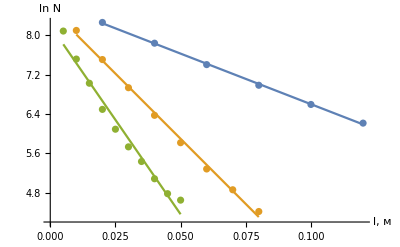

```mathematica
data1=Table[{0.02n,dataset2[n,"lnnAl"]},{n,6}];
data2=Table[{0.01n,dataset2[n,"lnnFe"]},{n,8}];
data3=Table[{0.005n,dataset2[n,"lnnPb"]},{n,10}];
fit1=LinearModelFit[data1,{1,x},x](*   f = a + b * x   *)
fit1["ParameterTable"];
a1=Around[fit1["BestFitParameters"]⟦1⟧,fit1["ParameterErrors"]⟦1⟧]
b1=Around[fit1["BestFitParameters"]⟦2⟧,fit1["ParameterErrors"]⟦2⟧]
fit2=LinearModelFit[data2,{1,x},x](*   f = a + b * x   *)
fit2["ParameterTable"];
a2=Around[fit2["BestFitParameters"]⟦1⟧,fit2["ParameterErrors"]⟦1⟧]
b2=Around[fit2["BestFitParameters"]⟦2⟧,fit2["ParameterErrors"]⟦2⟧]
fit3=LinearModelFit[data3,{1,x},x](*   f = a + b * x   *)
fit3["ParameterTable"];
a3=Around[fit3["BestFitParameters"]⟦1⟧,fit3["ParameterErrors"]⟦1⟧]
b3=Around[fit3["BestFitParameters"]⟦2⟧,fit3["ParameterErrors"]⟦2⟧]
(*fit["BestFitParameters"]⟦1⟧
fit["BestFitParameters"]⟦2⟧*)
(*hiTeXForm[a]
hiTeXForm[b]*)
Show[ListPlot[{data1,data2,data3},AxesLabel->{"l, м","ln N"}],Plot[fit1["BestFitParameters"]⟦1⟧+fit1["BestFitParameters"]⟦2⟧x,{x,Min[data1⟦All,1⟧],Max[data1⟦All,1⟧]}],Plot[fit2["BestFitParameters"]⟦1⟧+fit2["BestFitParameters"]⟦2⟧x,{x,Min[data2⟦All,1⟧],Max[data2⟦All,1⟧]},PlotStyle->ColorData[97,"ColorList"][[2]]],
Plot[fit3["BestFitParameters"]⟦1⟧+fit3["BestFitParameters"]⟦2⟧x,{x,Min[data3⟦All,1⟧],Max[data3⟦All,1⟧]},PlotStyle->ColorData[97,"ColorList"][[3]]]]
```

```mathematica
(Around[1,.2]+Around[1,.1]+Around[.8,.1])/3
```

0.930.08